#### Assignment 1. Three slash-dot tasks

(a) Use slash-dot notation to figure out what this complicated expression is equal to when x is 4:  1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2)).  
(b) Figure out the expression in terms of y, given x = 2y (and simplify your result)
(c) Define the following two expressions: y_1=x sin(x) and y_2=e^x. When plotted, the two curves intersect in an infinite number of places. Use FindRoot to find the intersection that occurs closest to x=0, and use slash-dot to determine what the y-value of the intersection is without doing any copying & pasting of your own.

```mathematica
(* (a) *)
g[x]=1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2))

g[x] /. x-> 4
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

1/65

```mathematica
(* (b) *)
g[x] /. x -> 2y
Simplify[%]
```

1/(3 (1+2 y))-(-1+4 y)/(6 (1-2 y+4 y^2))+2/(3 (1+1/3 (-1+4 y)^2))

```mathematica
(* (c) *)
y1[x] = x*Sin[x];
y2 [x] = E^x;
x /. FindRoot[y1[x] == y2[x], {x,0}]
```

-0.727101

#### Assignment 2. Postfix and prefix calculations

(a) Calculate the numerical value of log(sin(sqrt(exp(7.3)))) using standard commands.
(b) Repeat, using only postfix commands.
(c) Repeat, using prefix form

```mathematica
(* (a) *)
Log[Sin[Sqrt[Exp[7.3]]]]
```

-0.356515

```mathematica
(* (b) *)
7.3 // Exp // Sqrt // Sin // Log
```

-0.356515

```mathematica
(* (c) *)
Log@Sin@Sqrt@Exp@7.3
```

-0.356515

#### Assignment 3. Using FindRoot to solve a transcendental equation... and using the result

Let x0 represent the value of x for which x = e^-x. This is a transcendental equation, an equation that has no closed-form solution (i.e. you can’t write an equation for x).  Determine x0 with FindRoot, and then calculate sin(x0) using slash-dot (and no copy-and-paste). Hint: when solving transcendental equations it's always good to start with a graph of the functions that represent the left and right hand sides of the equation, to give you a rough idea of the answer. The solution x0 is where the functions intersect, because that’s the place where the left and right hand sides of the equation equal each other.

```mathematica
a3[x]=Exp[-x]
x0 = FindRoot[a3[x]==x,{x,0}]
```

ⅇ^-x

{x→0.567143}

```mathematica
Sin[x0]
N[%]
```

{Sin[x→0.567143]}

{Sin[x→0.567143]}

```mathematica
Plot[{x0},{x,0,10},PlotRange->All]
```

-Graphics-

Assignment 4: Derivatives

For each of the following, use a single D command:
(a) Find the decimal value of the second derivative of f(x) = 1/√(x^2+2), evaluated at x = 2.

(b) Plot P_3(x) along with its first derivative, from 0 to 20. Plot the P_3 function in blue and the derivative in red. P_n(x) is the “nth Legendre polynomial,” where Legendre polynomials are special functions which crop up in the solutions to the Schrodinger equation in 3 dimensions.  These are built-in functions within Mathematica (see LegendreP in help files). 

(c) Plot √(1+x^2) along with d^3/dx^3 √(1+x^2) , from -4 to 4. Plot the function in blue and the derivative in orange. Use either the option PlotLegends → “Expressions” or PlotLabels → “Expressions” to identify each plot.

(d) Plot3D (sin^2(x+y))/(x+y) along with ∂/(∂y)(∂/(∂x)(sin^2(x+y))/(x+y)) (or equivalently  ∂^2/(∂x∂y)(sin^2(x+y))/(x+y), from -π to π on both the x- and the y-axes. Plot the function in blue and the derivative in orange.

```mathematica
(* (a) *)
a4[x] = 1/(Sqrt[x^2 +2]);
D[a4[x],x,x] /. x->4;
Simplify[%]
```

5/(162 √2)

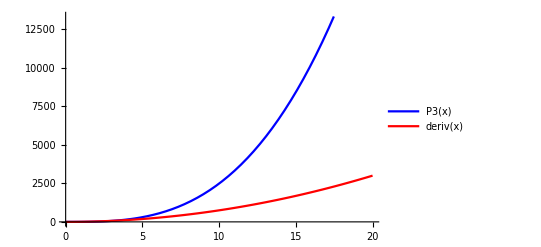

```mathematica
(* (b) *)
P3[x]=LegendreP[3,x];
deriv[x] = D[P3[x],x];
Plot[{P3[x],deriv[x]},{x,0,20},PlotStyle->{Blue,Red}, PlotLegends->"Expressions"]
```

```mathematica
(* (c) *)
c1[x] = Sqrt[1+x^2];
cD3[x] = D[c1[x],x,x,x];
Simplify[%];
Plot[{c1[x],cD3[x]},{x,-4,4}, PlotStyle->{Blue,Orange}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
(* (d) *)
d1[x,y]=((Sin[x+y])^2)/(x+y);
d2[x,y] = D[d1[x,y],x,y];
Simplify[%];
Plot3D[{d1[x,y],d2[x,y]},{x,Pi,-Pi},{y,Pi,-Pi},PlotStyle->{Blue,Orange}]
```

-Graphics3D-

#### Assignment 5. Converting between exponential and sin/cos forms

(a) Use ExpToTrig to convert e^ix into trigonometric form, to verify that Mathematica “knows” Euler’s formula.
(b) Use ExpToTrig to convert e^x into trigonometric form. This is the analog of Euler’s formula for hyperbolic functions sinh(x) and cosh(x).
(c) Use TrigToExp to convert cos(x) and sin(x) into exponential form.
(d) Use TrigToExp to convert cosh(x) and sinh(x) into exponential form. Notice the similarity to the exponential forms of cosine and sine.
(e) Use Mathematica to take the complex conjugate of e^ix and then show that it is equal to cos(x)-isin(x) (rather than the awkward “cos[Conjugate[x]]- i sin[Conjugate[x]]”).  Don’t make explicit use of Assumptions to define x as real.

```mathematica
(* (a) *)
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

```mathematica
(* (b) *)
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

```mathematica
(* (c) *)
TrigToExp[Cos[x]]
TrigToExp[Sin[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
(* (d) *)
TrigToExp[Cosh[x]]
TrigToExp[Sinh[x]]
```

ⅇ^-x/2+ⅇ^x/2

-ⅇ^-x/2+ⅇ^x/2

```mathematica
(* (e) *)
Conjugate[Exp[I*x]]
Simplify[%]
TrigToExp[Cos[x]-I*Sin[x]]
```

ⅇ^(-ⅈ Conjugate[x])

ⅇ^(-ⅈ Conjugate[x])

ⅇ^(-ⅈ x)

What to turn in
When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#4a-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 5).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.